RateL2R[0.5,0.025,0.13,1.]

RateR2L[0.5,0.025,0.13,1.]

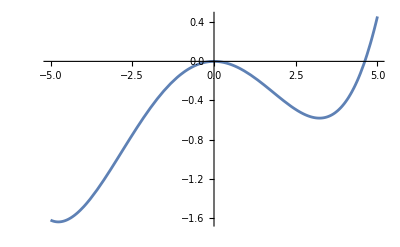

```mathematica
(*Explicit Arrhenius rates for V[ψ]=-(1/2) μ^2 ψ^2+(2/3) β3 μ ψ^3+(1/4) (β4^2-β3^2) ψ^4*)
ClearAll["Global`*"];
(*Assumptions:stable quartic,two real minima,de Sitter H>0*)
Assums=mu>0&&H>0&&λ>0&&beta3>0&&beta4>Abs[beta3];
V[ψ_,mu_,beta3_,beta4_]:=-(mu^2 ψ^2)/2+(2 beta3 mu ψ^3)/3+(beta4^2-beta3^2) ψ^4/4;
(*Use a dummy variable x in D to avoid "invalid variable" issues*)
V1[ψ_,mu_,beta3_,beta4_]:=Evaluate[D[V[x,mu,beta3,beta4],x]/. x->ψ];
(*Explicitly:-mu^2 ψ+2 beta3 mu ψ^2+(beta4^2-beta3^2) ψ^3*)
V2[ψ_,mu_,beta3_,beta4_]:=Evaluate[D[V[x,mu,beta3,beta4],{x,2}]/. x->ψ];
(*Explicitly:-mu^2+4 beta3 mu ψ+3 (beta4^2-beta3^2) ψ^2*)
(*Stationary points:analytic for this potential.For beta4> |beta3|:barrier at ψ=0,left (deeper) minimum at ψ=-mu/(beta4-beta3),right (shallower) minimum at ψ=mu/(beta4+beta3).*)

ψBarrier[mu_,beta3_,beta4_]:=0;
ψTrue[mu_,beta3_,beta4_]:=-mu/(beta4-beta3);
ψFalse[mu_,beta3_,beta4_]:=mu/(beta4+beta3);

(*Barrier heights above each minimum*)

DeltaL2R[mu_,beta3_,beta4_]:=V[ψBarrier[mu,beta3,beta4],mu,beta3,beta4]-V[ψTrue[mu,beta3,beta4],mu,beta3,beta4];
DeltaR2L[mu_,beta3_,beta4_]:=V[ψBarrier[mu,beta3,beta4],mu,beta3,beta4]-V[ψFalse[mu,beta3,beta4],mu,beta3,beta4];
(*Kramers prefactors (de Sitter Hawking–Moss style)*)
PreL2R[mu_,beta3_,beta4_,H_]:=1/(6 H^2 π) Sqrt@Abs[V2[ψBarrier[mu,beta3,beta4],mu,beta3,beta4]*V2[ψTrue[mu,beta3,beta4],mu,beta3,beta4]];
PreR2L[mu_,beta3_,beta4_,H_]:=1/(6 H^2 π) Sqrt@Abs[V2[ψBarrier[mu,beta3,beta4],mu,beta3,beta4]*V2[ψFalse[mu,beta3,beta4],mu,beta3,beta4]];
(*Arrhenius rates*)
RateT2F[mu_,beta3_,beta4_,H_]:=PreL2R[mu,beta3,beta4,H]*Exp[(-4 π^2 DeltaL2R[mu,beta3,beta4])/(3 H^4)];
RateF2T[mu_,beta3_,beta4_,H_]:=PreR2L[mu,beta3,beta4,H]*Exp[(-4 π^2 DeltaR2L[mu,beta3,beta4])/(3 H^4)];
(*Relaxation time from both directions*)
relaxationtime[mu_,beta3_,beta4_,H_]:=FullSimplify[1/(RateR2L[mu,beta3,beta4,H]+RateL2R[mu,beta3,beta4,H]),Assums];
(*Optional:dimensionless curvatures m_eff^2/H^2 at the three stationary points*)
curvTrue[mu_,beta3_,beta4_,H_]:=FullSimplify[V2[ψTrue[mu,beta3,beta4],mu,beta3,beta4]/H^2,Assums];
curvFalse[mu_,beta3_,beta4_,H_]:=FullSimplify[V2[ψFalse[mu,beta3,beta4],mu,beta3,beta4]/H^2,Assums];
curvBarrier[mu_,beta3_,beta4_,H_]:=FullSimplify[V2[ψBarrier[mu,beta3,beta4],mu,beta3,beta4]/H^2,Assums];
(*Example numeric checks with your paper values:mu=0.5,beta3=0.025,beta4=0.13,H=1*)
RateL2R[0.5,0.025,0.13,1.]//N
RateR2L[0.5,0.025,0.13,1.]//N
Plot[V[ψ,0.5,0.025,0.13],{ψ,-5,5}]
```

```mathematica
Clear[β3 ,β4]
FullSimplify[1/RateF2T[μ,β3,β4,H],{μ>0,β3>0,β4>0,β4>β3,H>0}]
FullSimplify[1/RateT2F[μ,β3,β4,H],{μ>0,β3>0,β4>0,β4>β3,H>0}]
```

(3 √2 ⅇ^((π^2 (β3+3 β4) μ^4)/(9 H^4 (β3+β4)^3)) H^2 π √((β3+β4)/β4))/μ^2

(3 ⅇ^((π^2 (β3-3 β4) μ^4)/(9 H^4 (β3-β4)^3)) H^2 π √(2-(2 β3)/β4))/μ^2

```mathematica
MFPTF2T[μt_]=(3 √2 ⅇ^((π^2 (β3+3 β4)μt^4)/(9  (β3+β4)^3))  π √((β3+β4)/β4))/μt^2
MFPTT2F[μt_]=(3 ⅇ^((π^2 (β3-3 β4) μt^4)/(9  (β3-β4)^3))  π √(2-(2 β3)/β4))/μt^2
```

(3 √2 ⅇ^((π^2 (β3+3 β4) μt^4)/(9 (β3+β4)^3)) π √((β3+β4)/β4))/μt^2

(3 ⅇ^((π^2 (β3-3 β4) μt^4)/(9 (β3-β4)^3)) π √(2-(2 β3)/β4))/μt^2

```mathematica
Solve[MFPTF2T'[μt]==0,μt]
```

{{μt→-(√(3/π) (β3+β4)^(3/4))/(2 β3+6 β4)^(1/4)},{μt→-(ⅈ √(3/π) (β3+β4)^(3/4))/(2 β3+6 β4)^(1/4)},{μt→(ⅈ √(3/π) (β3+β4)^(3/4))/(2 β3+6 β4)^(1/4)},{μt→(√(3/π) (β3+β4)^(3/4))/(2 β3+6 β4)^(1/4)}}